```mathematica
mu=0.25;
n=100;
delta=2Pi/n;
lambda=delta^2;

states={};

For[i=0,i≤n-1,i++,
kx=-Pi+i*delta;
list={};

For[j=0,j≤n-1,j++,
ky=-Pi+j*delta;

H={{1+2*mu*(Cos[kx]+Cos[ky]),-2*mu*(Sin[kx]+I*Sin[ky])},{-2*mu*(Sin[kx]-I*Sin[ky]),-(1+2*mu*(Cos[kx]+Cos[ky]))}};
a=Eigenvectors[H,-1];

AppendTo[list,a];
];

AppendTo[states,list];
]
```

```mathematica
x[i_]:=Mod[i,n];
y[j_]:=Mod[j,n];
gamma={};

For[i=0,i≤n-1,i++,

For[j=0,j≤n-1,j++,
b=Conjugate[states[[x[i]+1,y[j]+1,1]]].states[[x[i+1]+1,y[j]+1,1]];
r=Conjugate[states[[x[i+1]+1,y[j]+1,1]]].states[[x[i+1]+1,y[j+1]+1,1]];
u=Conjugate[states[[x[i+1]+1,y[j+1]+1,1]]].states[[x[i]+1,y[j+1]+1,1]];
l=Conjugate[states[[x[i]+1,y[j+1]+1,1]]].states[[x[i]+1,y[j]+1,1]];

AppendTo[gamma,Arg[b]+Arg[r]+Arg[u]+Arg[l]];
];
]

Total[gamma]/(2*Pi)
Dimensions[gamma]
MatrixPlot[Partition[gamma,n],PlotLegends->Automatic]
```

1.

{10000}

-Graphics-

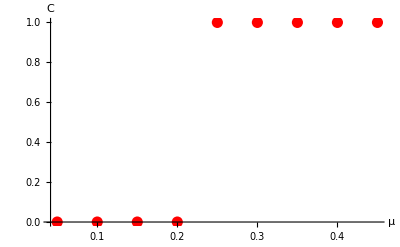

```mathematica
data=Import["C:\\Users\\matte\\Desktop\\Ph.D\\Solid state problems\\Berry phases\\Chern-number.txt","Table"];
ListPlot[data,PlotStyle->{Red,PointSize[.02]},AxesLabel->{"μ","C"},AxesStyle->Directive[Black, 12],PlotRange->All]
```